2.)

```mathematica
N@Length[
Select[
Table[RandomSample[setDeck,3],50000], 
setCheck[#]&
]
]/50000
```

0.0126

```mathematica
N[1/79]
```

0.0126582

The probability generated in Mathematica is about the same as 1/79, confirming our answer is correct.

4.)

```mathematica
N@Length[
Select[
Table[
Map[
setCheck[#]&,
Flatten[{Subsets[RandomSample[setDeck,4],{3}]},1]
],
1000000
],
MemberQ[#,True]&
]
]/1000000
```

0.050761

```mathematica
N[4/79]
```

0.0506329

The probability generated in Mathematica is about the same as 4/79, confirming our prediction is correct.

5.)

```mathematica
SortBy[
Map[
Join[#,{N@#[[2]]/1000}]&,
Tally[
Table[
Select[
Subsets[
RandomSample[setDeck,12],
{3}
],
setCheck[#]& (* checks for sets in group of 12 cards *)
]//Length, (* amount of sets *)
100000 (* gives number of sets 100000 times *)
]
]
],
#[[1]]&
]//TableForm
```

0 | 3215 | 3.215
1 | 14465 | 14.465
2 | 25939 | 25.939
3 | 27303 | 27.303
4 | 17939 | 17.939
5 | 8035 | 8.035
6 | 2550 | 2.55
7 | 473 | 0.473
8 | 60 | 0.06
9 | 17 | 0.017
10 | 2 | 0.002
11 | 1 | 0.001
12 | 1 | 0.001

6.(c)

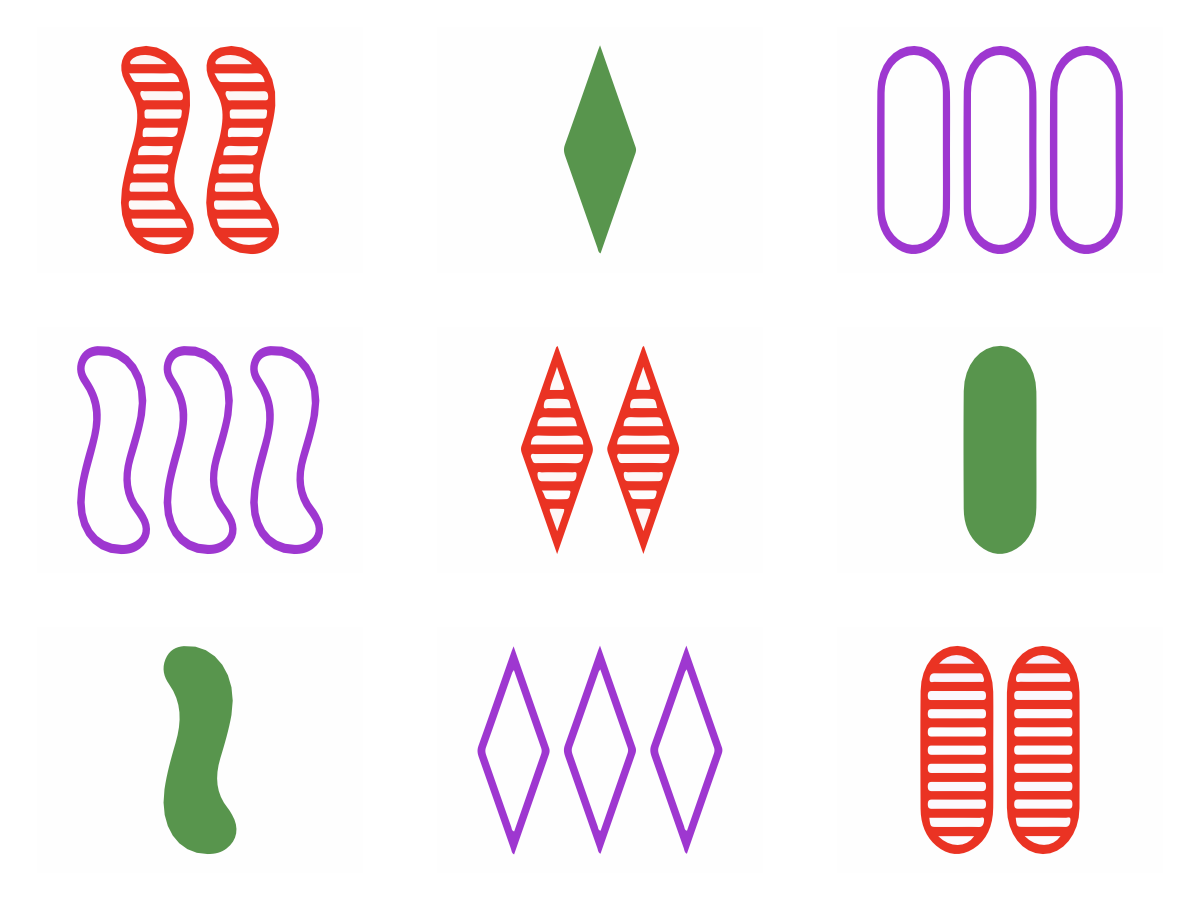

```mathematica
Map[setToImage[#]&,planeMaker[{{2,Red,striped,squiggle},{1,Green,solid,diamond},{3,Purple,empty,squiggle}}]]//TableForm
```

7.(b)

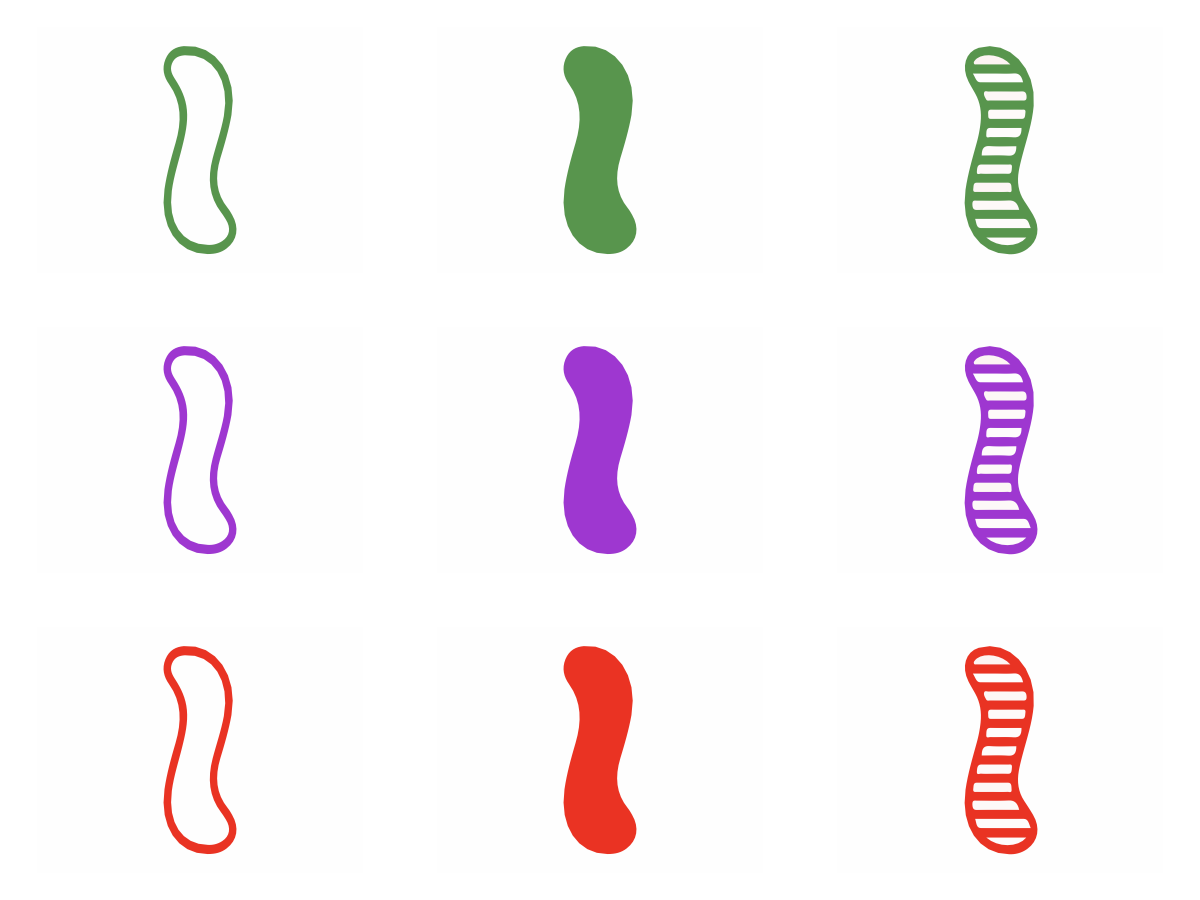
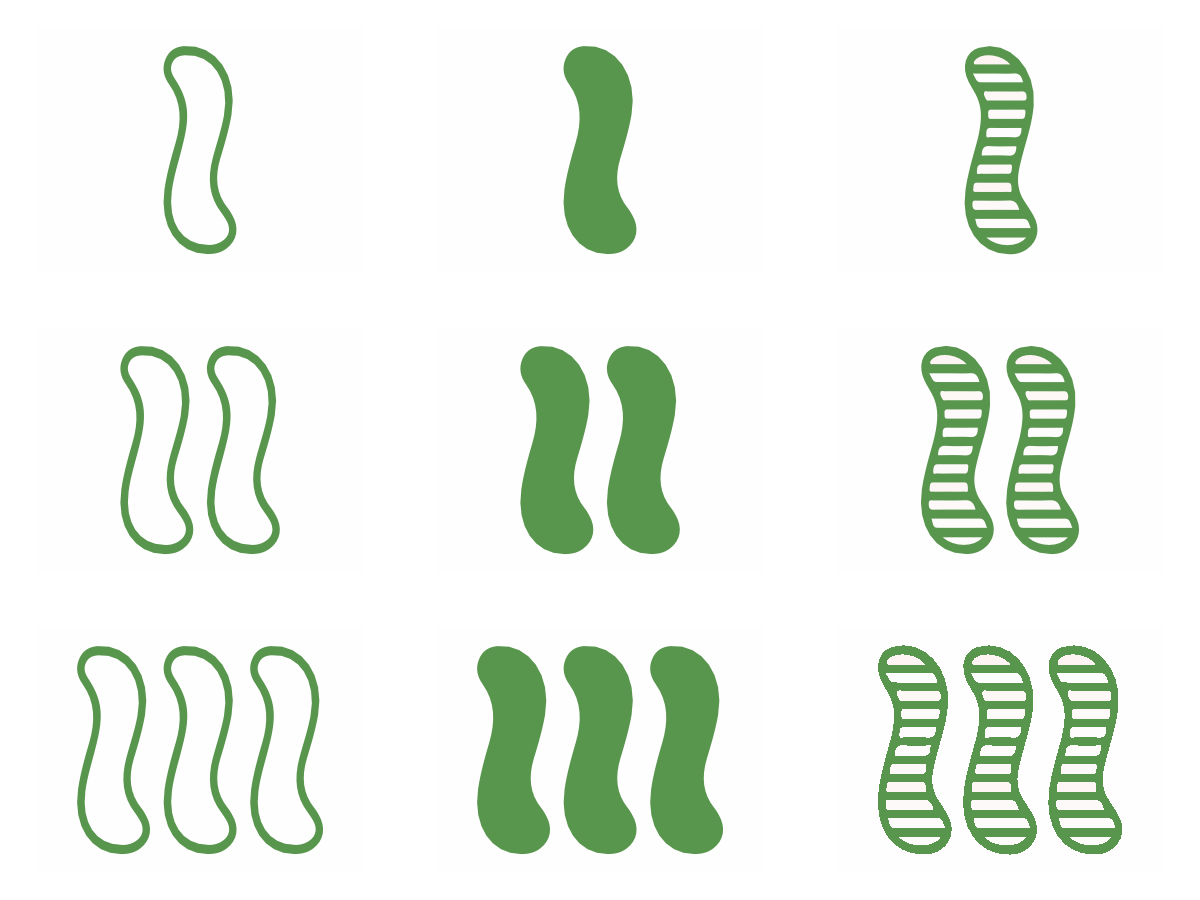
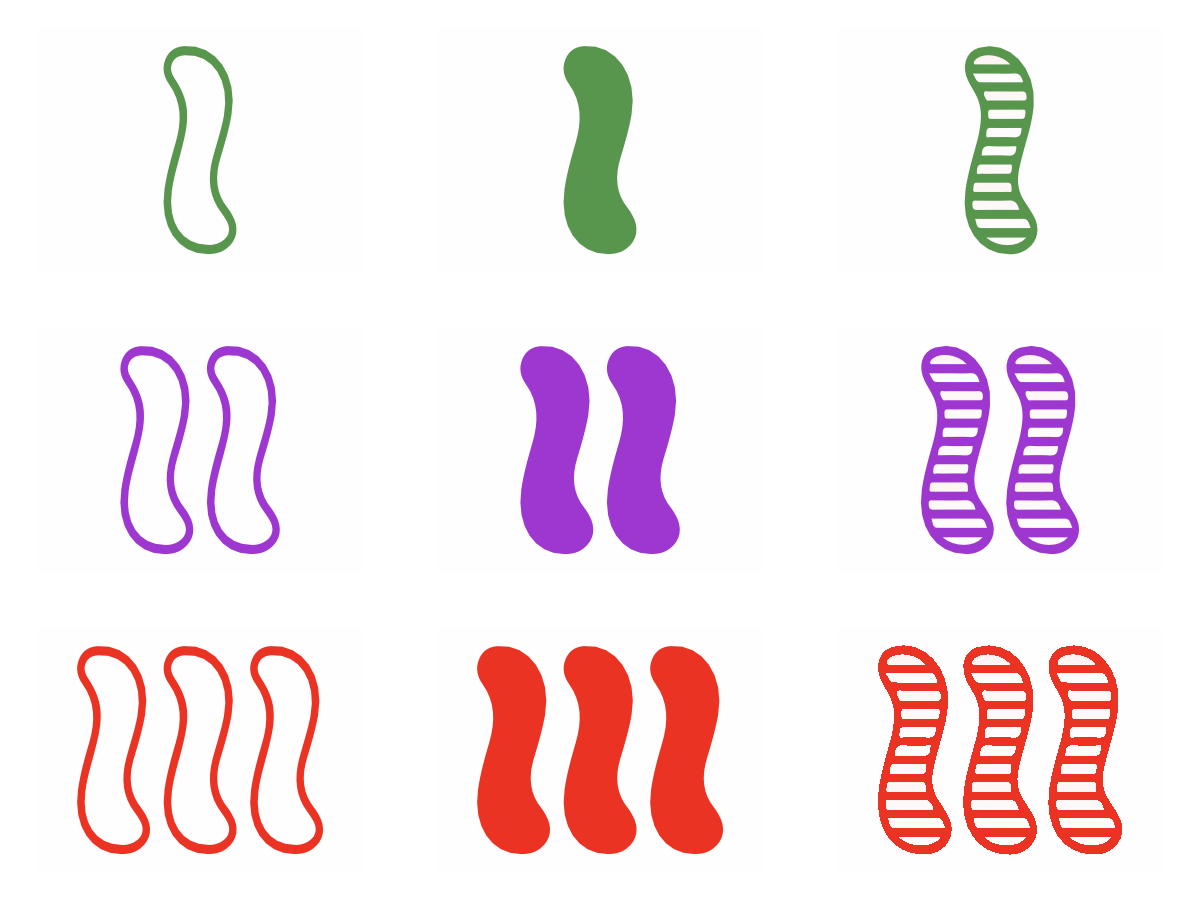
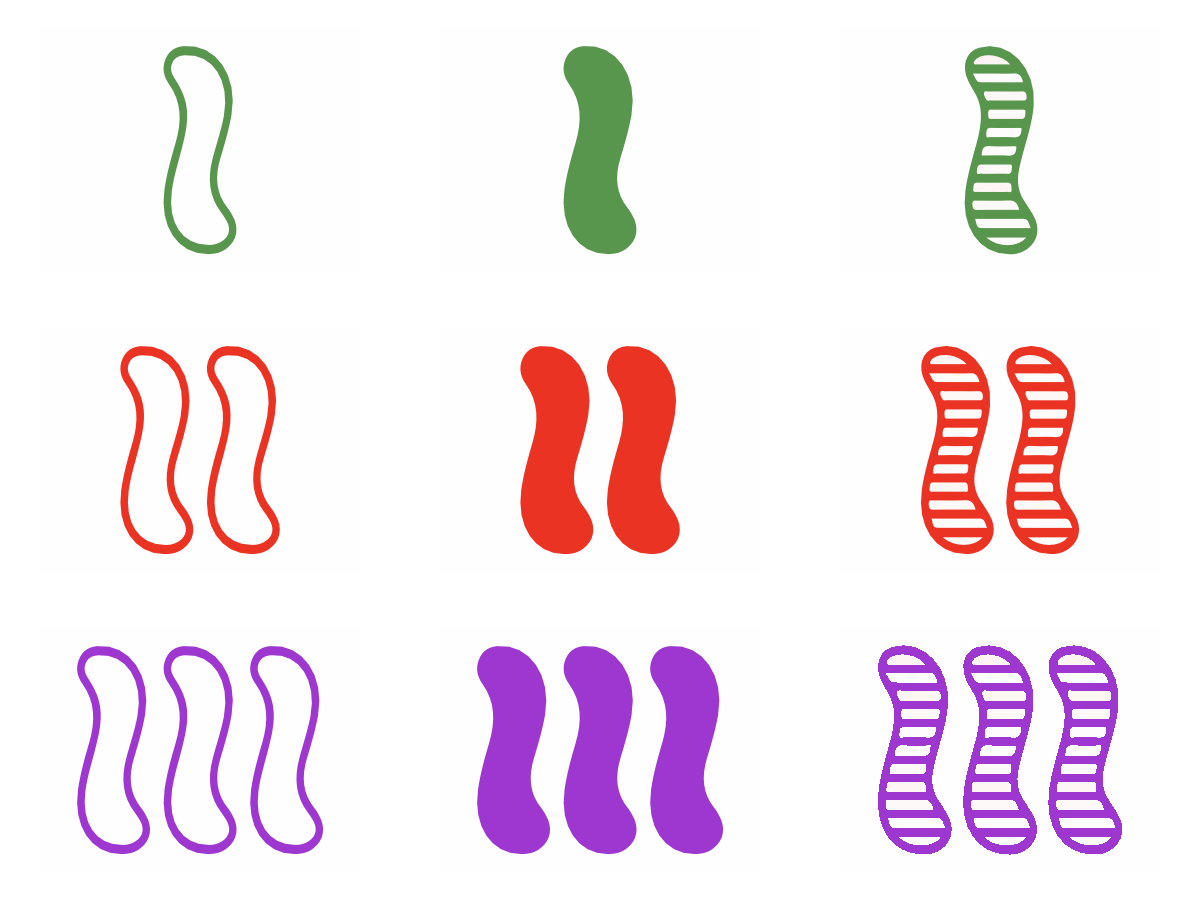
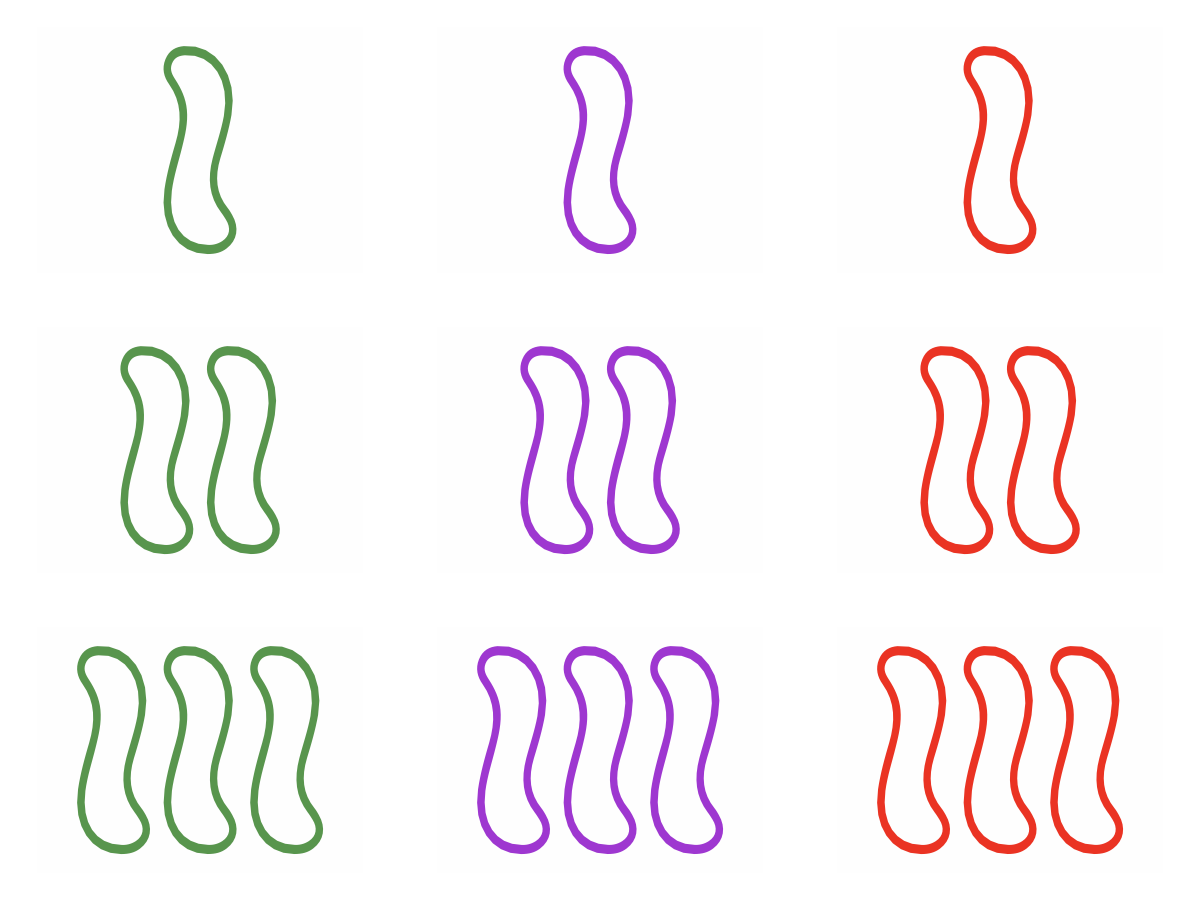
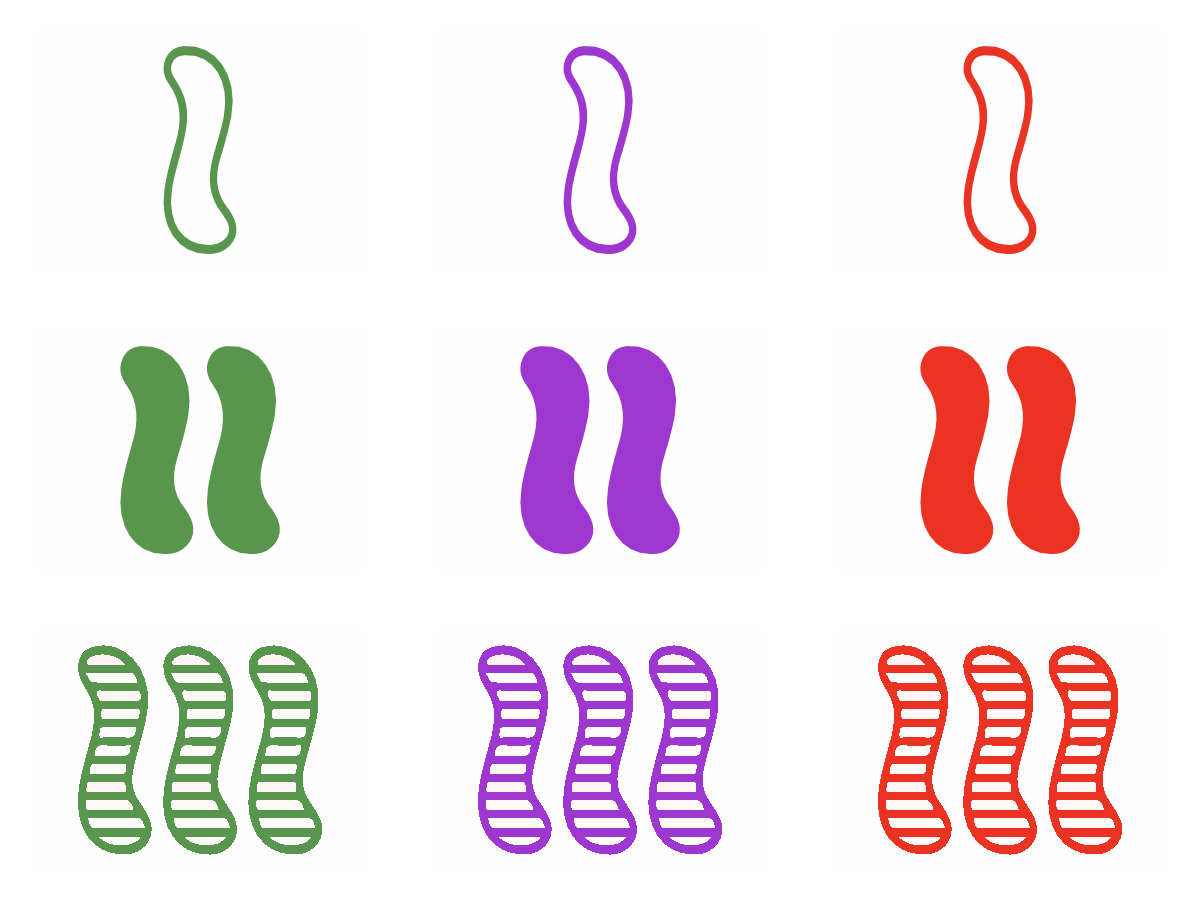
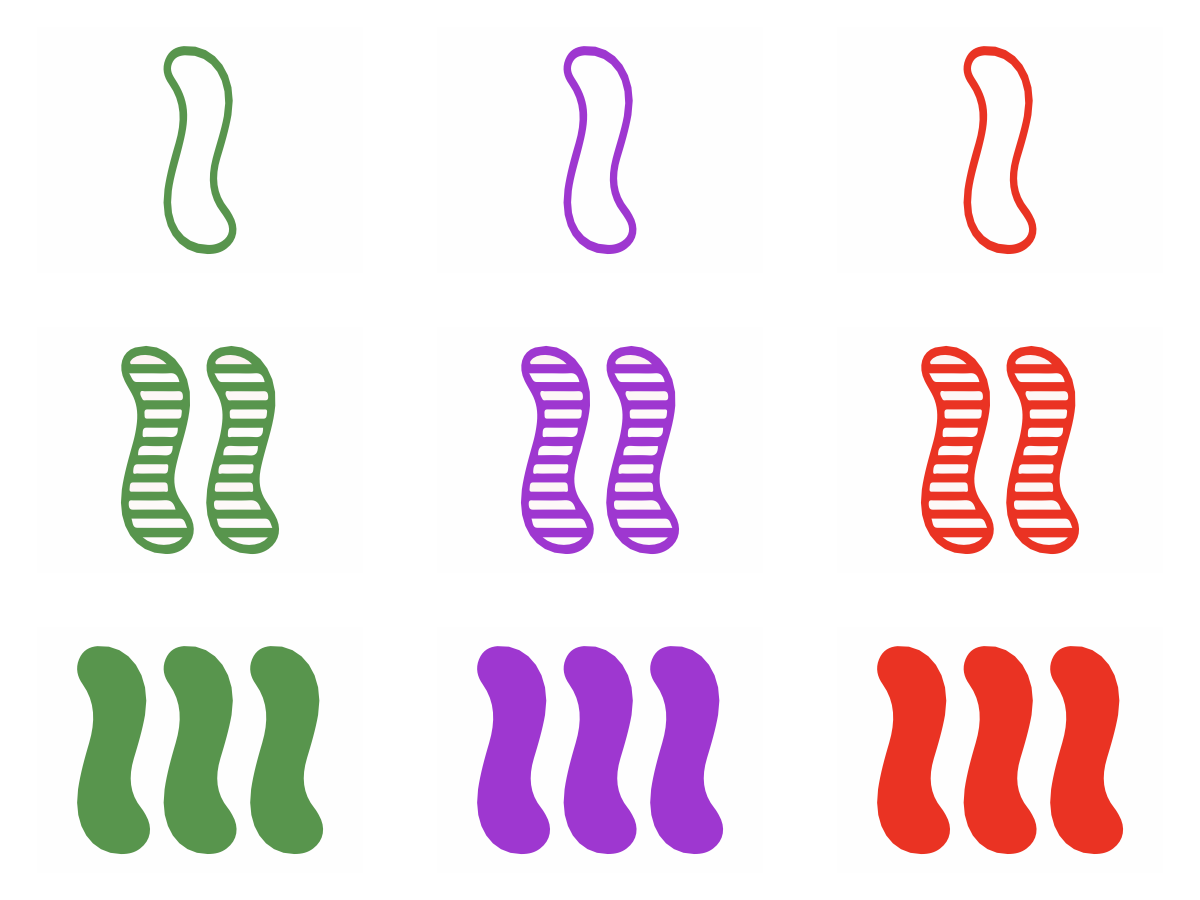
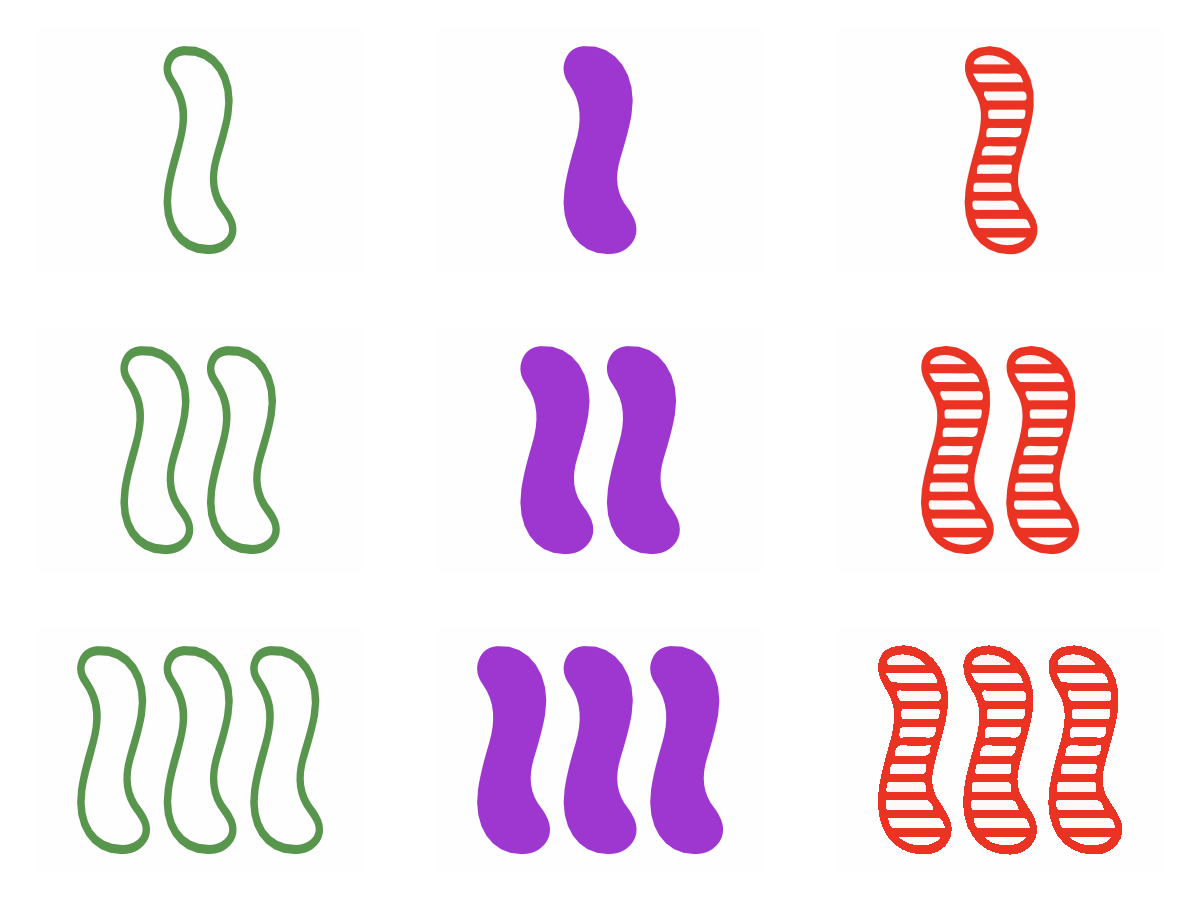
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Magnify[
TableForm[
Partition[
Map[
Partition[#,3]&,
Map[
setToImage[#]&,
Select[
allPlanes,
#[[1]][[4]]== squiggle&&
#[[2]][[4]]==squiggle&&
#[[4]][[4]]==squiggle&
]
]
],
3
],
TableSpacing->{10, 10}
],
1/4
]
```